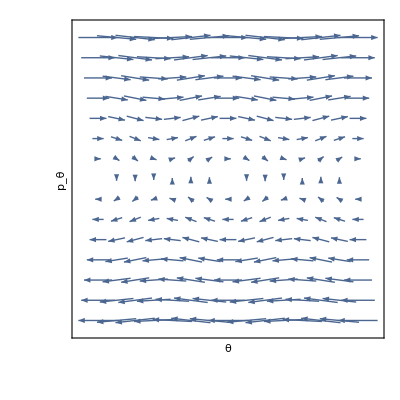

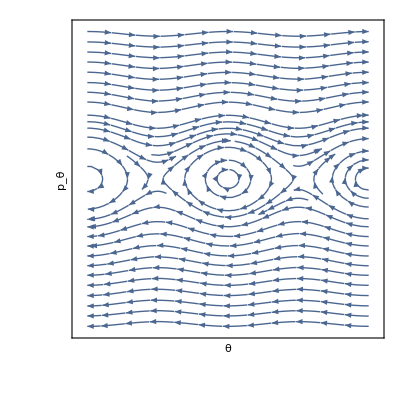

```mathematica
m =1;
MOI =0.25;
d = 1;
g=9.81;
vec[p_,th_]:={p/MOI,-m g d Sin[th]}
Show[VectorPlot[vec[p,th],{th,-2Pi,2Pi},{p,-12,12}],AxesLabel->{None,None},FrameLabel->{{HoldForm[Subscript[p, θ]],None},{HoldForm[θ],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]},FrameTicks->{None,None}]

Show[StreamPlot[vec[p,th],{th,-2Pi,2Pi},{p,-12,12}],AxesLabel->{None,None},FrameLabel->{{HoldForm[Subscript[p, θ]],None},{HoldForm[θ],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]},FrameTicks->{None,None}]
```

```mathematica
vec[p,th]
```

{-9.81 Sin[th],p}